```mathematica
ClearAll[x,y,t,z]
```

# 10.2B Homework

## Problem 1:

```mathematica
F[t_] := t*Cos[t];
G[t_] := t*Sin[t];
```

```mathematica
F[π]
G[π]
```

```mathematica
Subscript[x, 1]=-π;
```

```mathematica
Subscript[y, 1]=0;
```

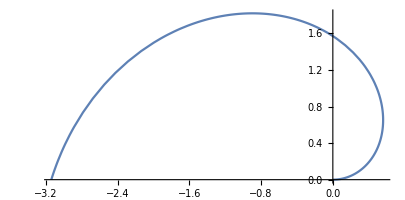

```mathematica
ParametricPlot[{F[t],G[t]},{t,0,π}]
```

```mathematica
(F'[t])^-1(G'[t])
```

```mathematica
H[t_]:=(t Cos[t]+Sin[t])/(Cos[t]-t Sin[t])
```

```mathematica
H[π] (* y-Subscript[y, 1] = m(x-Subscript[x, 1]) *)
```

π

```mathematica
Solve[y-Subscript[y, 1] == π(x-Subscript[x, 1]),y]
```

{{y→π (π+x)}}

## Problem 2:

```mathematica
(*Find the exact length of the curve.*)
```

```mathematica
ClearAll[x,y,t,F,G]
```

```mathematica
(*x*)F[t_]:= ⅇ^t+1/ⅇ^t;
(*y*)G[t_]:= 5 - 2*t;
∫_0^4 √((D[G[t],t])^2+(D[F[t],t])^2)ⅆt
```

2 Sinh[4]

## Problem 3:

```mathematica
(*Graph the curve*)
```

```mathematica
ClearAll[x,y,t,F,G]
```

```mathematica
F[t_]:=4 ⅇ^t*Cos[t];
G[t_] := 4 ⅇ^t*Sin[t];
```

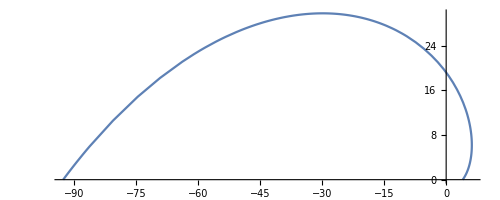

```mathematica
ParametricPlot[{F[t],G[t]},{t,0,π},AspectRatio->Automatic]
```

```mathematica
∫_0^π √((F'[t])^2+(G'[t])^2)ⅆt
```

4 √2 (-1+ⅇ^π)

## Problem 4:

```mathematica
(*Find the surface area generated by rotating the given curve about the y-axis.*)
```

```mathematica
ClearAll[F,G,x,y,t]
```

```mathematica
Reduce[ x== ⅇ^t-t,t]
```

```mathematica
F[t_] := ⅇ^t-t;
G[t_] := 4*ⅇ^(t/2);
2π∫_0^3 F[t]*√((F'[t])^2+(G'[t])^2)ⅆt
```

2 (-7-ⅇ^3+ⅇ^6/2) π

## Problem 5:

```mathematica
(*find dy/dx and d^2y/dx^2 *)
```

```mathematica
ClearAll[x,y,t,F,G,H]
```

```mathematica
F[t_]:= t^2+6;
G[t_] := t^2+3*t;

D[G[t],t]/D[F[t],t]
```

```mathematica
H[t_]:=(3+2 t)/(2 t);
```

```mathematica
H'[t]
```

1/t-(3+2 t)/(2 t^2)

```mathematica
Simplify[1/t-(3+2 t)/(2 t^2)]
```

-3/(2 t^2)

## Problem 7:

```mathematica
Solve[10==6 t^2+4,t]
```

{{t→-1},{t→1}}

```mathematica
Eliminate[{x==6 t^2+4,y==4 t^3+4},{t}]
```

560-216 y+27 y^2==96 x-24 x^2+2 x^3

```mathematica
Solve[560-216 y+27 y^2==96 x-24 x^2+2 x^3,y]
```

{{y→1/9 (36-√6 √(-64+48 x-12 x^2+x^3))},{y→1/9 (36+√6 √(-64+48 x-12 x^2+x^3))}}

```mathematica
ClearAll["Global`*"]
```

```mathematica
F[x_]:=1/9 (36-√6 √(-64+48 x-12 x^2+x^3));
```

```mathematica
G[x_]:=1/9 (36+√6 √(-64+48 x-12 x^2+x^3));
```

```mathematica
LinearF[x_]:=(x-10)+8
```

```mathematica
LinearG[x_]:= 18-x;
```

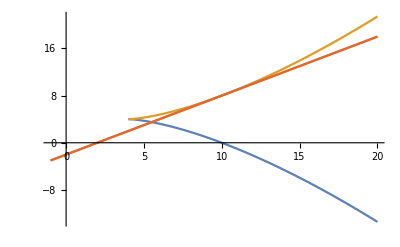

```mathematica
Plot[{F[x],G[x],LinearF[x],-LinearG[x]+16},{x,-1,20}]
```

```mathematica
F'[10]
G'[10]
```

-1

1

```mathematica
Solve[y-8==-(x-10),y]
```

{{y→18-x}}

```mathematica
(*y=-x+18*)
```